```mathematica
ClearAll["Global`*"]
```

```mathematica
table0171 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,17_1.txt",{"Table", "Data"}];
table0171[[All,1]]=table0171[[All,1]]-table0171[[1,1]];
table0171[[All,2]]=((table0171[[All,2]]+0.002)/(0.0043×0.20827));
table0171[[All,2]]=table0171[[All,2]]-Min[table0171[[All,2]]];
```

```mathematica
table0172 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,17_2.txt",{"Table", "Data"}];
table0172[[All,1]]=table0172[[All,1]]-table0172[[1,1]];
table0172[[All,2]]=((table0172[[All,2]]+0.002)/(0.0043×0.20827));
table0172[[All,2]]=table0172[[All,2]]-Min[table0172[[All,2]]];
```

```mathematica
table0173 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,17_3.txt",{"Table", "Data"}];
table0173[[All,1]]=table0173[[All,1]]-table0173[[1,1]];
table0173[[All,2]]=((table0173[[All,2]]+0.002)/(0.0043×0.20827));
table0173[[All,2]]=table0173[[All,2]]-Min[table0173[[All,2]]];
```

```mathematica
table0174 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,17_4.txt",{"Table", "Data"}];
table0174[[All,1]]=table0174[[All,1]]-table0174[[1,1]];
table0174[[All,2]]=((table0174[[All,2]]+0.002)/(0.0043×0.20827));
table0174[[All,2]]=table0174[[All,2]]-Min[table0174[[All,2]]];
```

```mathematica
table0175 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,17_5.txt",{"Table", "Data"}];
table0175[[All,1]]=table0175[[All,1]]-table0175[[1,1]];
table0175[[All,2]]=((table0175[[All,2]]+0.002)/(0.0043×0.20827));
table0175[[All,2]]=table0175[[All,2]]-Min[table0175[[All,2]]];
```

```mathematica
Export["table0171.dat",table0171];Export["table0172.dat",table0172];Export["table0173.dat",table0173];Export["table0174.dat",table0174];Export["table0175.dat",table0175];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit0171=FindFit[table0171,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→1.65462,T0→72.7801,Tout→1.11065}

```mathematica
fit0172=FindFit[table0172,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→1.04514,T0→46.3086,Tout→0.355752}

```mathematica
fit0173=FindFit[table0173,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→1.10574,T0→42.7749,Tout→0.34167}

```mathematica
fit0174=FindFit[table0174,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.964539,T0→44.5082,Tout→1.20986}

```mathematica
fit0175=FindFit[table0175,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→1.03469,T0→39.3735,Tout→0.337732}

```mathematica
k0171=Mean[{k/.fit0171,k/.fit0172,k/.fit0173,k/.fit0174,k/.fit0175}]
```

1.16094

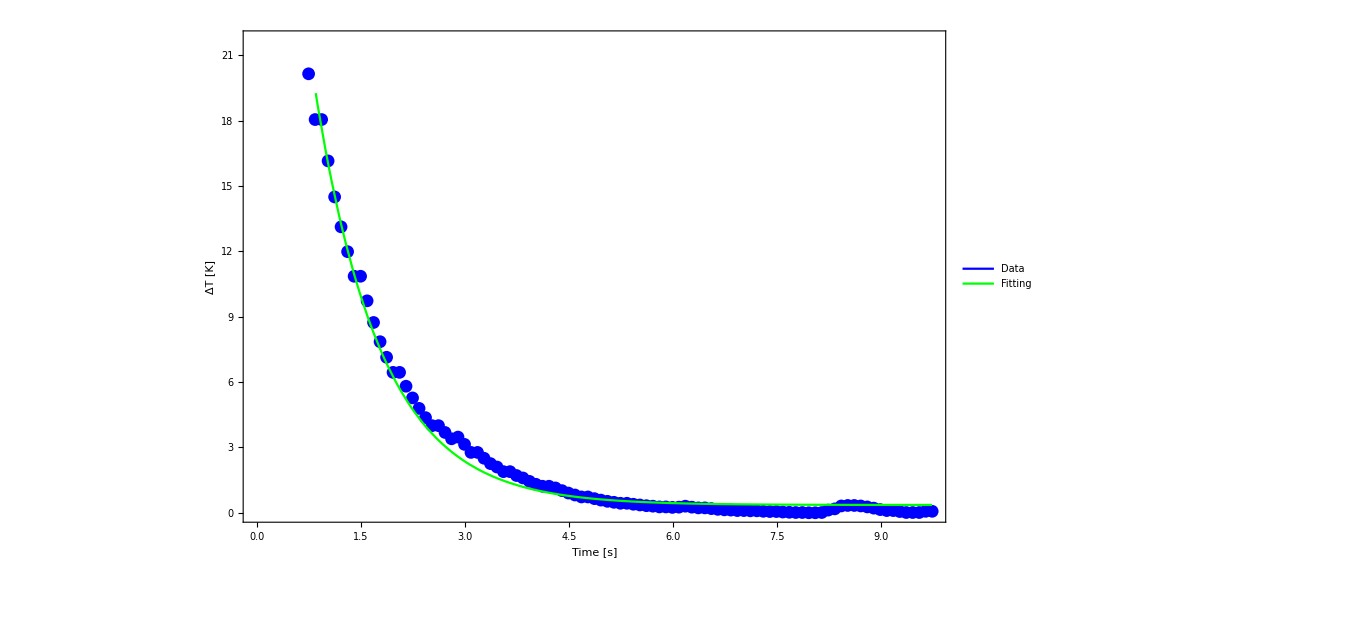

```mathematica
Legended[Show[ListPlot[table0172,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit0172,{t,0,Max[table0172[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```